```mathematica
Factor[x^5-1]
```

(-1+x) (1+x+x^2+x^3+x^4)

```mathematica
TrigReduce[Sin[θ]^3]
```

1/4 (3 Sin[θ]-Sin[3 θ])

```mathematica
p=Exists[x,a x^2+b x+c==0,ForAll[y,a y^2+b y+c==0,x==y]]
```

∃_(x,c+b x+a x^2==0)(∀_(y,c+b y+a y^2==0)x==y)

```mathematica
Reduce[p]
```

(a==0&&b≠0)||(a==0&&b c≠0)||(c==0&&b==0&&a≠0)||(c≠0&&a==b^2/(4 c)&&b≠0)

```mathematica
Piecewise[{{1,x==0}},Sin[x]/x]
```

Piecewise[{{1, x==0}, {Sin[x]/x, True}}]

```mathematica
Solve[x^3-a x+1==0,x]
```

{{x→((2/3)^(1/3) a)/((-9+√3 √(27-4 a^3))^(1/3))+((-9+√3 √(27-4 a^3))^(1/3))/(2^(1/3) 3^(2/3))},{x→-((1+ⅈ √3) a)/(2^(2/3) 3^(1/3) (-9+√3 √(27-4 a^3))^(1/3))-((1-ⅈ √3) (-9+√3 √(27-4 a^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{x→-((1-ⅈ √3) a)/(2^(2/3) 3^(1/3) (-9+√3 √(27-4 a^3))^(1/3))-((1+ⅈ √3) (-9+√3 √(27-4 a^3))^(1/3))/(2 2^(1/3) 3^(2/3))}}

```mathematica
∫1/(1+x^4)ⅆx
```

1/(4 √2)(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[-1+√2 x-x^2]+Log[1+√2 x+x^2])

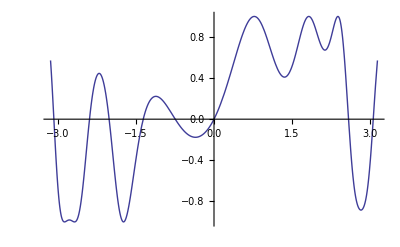

```mathematica
Plot[Sin[x+√2 Sin[x^2]],{x,-π,π}]
```

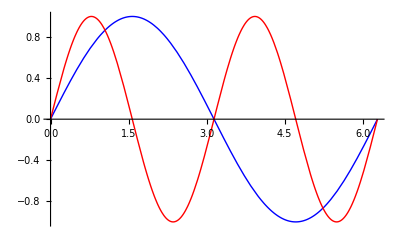

```mathematica
Plot[{Sin[x],Sin[2x]},{x,0,2π},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0]}]
```

```mathematica
ρ=Cos[ϕ]Sin[θ];
σ=Sin[ϕ]Sin[θ];
τ=0.2ϕ+Cos[θ]+Log[Tan[θ/2]];
ParametricPlot3D[{ρ,σ,τ},{ϕ,0,4π},{θ,.05,1},Axes->False,
Boxed->False,PlotPoints->30,AspectRatio->1.75]
```

-Graphics3D-

```mathematica
Divisors[1969]
```

{1,11,179,1969}

```mathematica
PerfectQ[n_]:=Apply[Plus,Divisors[n]]==2n
```

```mathematica
PerfectSearch[n_]:=Select[Range[n],PerfectQ]
```

```mathematica
PerfectSearch[10^6]
```

{6,28,496,8128}

```mathematica
vertices[n_Intger,r_:1]:=
Table[{r Cos[2α π/n],r Sin[2α π/n]},{α,0,n-1}]
```

```mathematica
RegularPolygon[n_]:=
Graphics[Line[vertices[n]/.{a_,b__}->{a,b,a}],
AspectRatio->Automatic]
```

```mathematica
Show[RegularPolygon[5]]
```

-Graphics-

```mathematica
<<Graphics`Polyhedra`
```

General::newpkg: "Graphics`Polyhedra`" is now available as the "Polyhedron Operations Package". See the Compatibility Guide for updating information.

```mathematica
Show[Stellate[Polyhedron[Iconsahedron]]]
```

Show::gtype: Polyhedron is not a type of graphics.

Show[Polyhedron[Iconsahedron]]

```mathematica
FullForm[{a,b,c}]
```

List[a,b,c]

```mathematica
FullForm[Sin[x](a x^2+b x+c)]
```

Times[Plus[c,Times[b,x],Times[a,Power[x,2]]],Sin[x]]

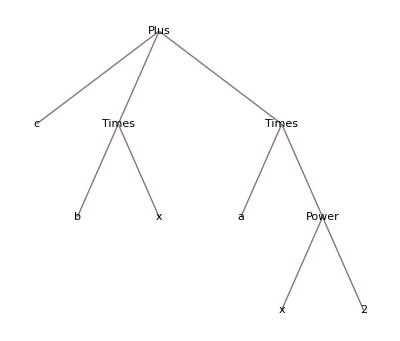

```mathematica
TreeForm[a x^2+b x+c]
```

```mathematica
?TreePlot
```

TreePlot[{v_i1->v_j1,v_i2->v_j2,…}] generates a tree plot of the graph in which vertex v_ik is connected to vertex v_jk.
TreePlot[{{v_i1->v_j1,lbl_1},…}] associates labels lbl_k with edges in the graph.
TreePlot[g,pos] places roots of trees in the plot at position pos.
TreePlot[g,pos,v_k] uses vertex v_k as the root node in the tree plot.

```mathematica
FullForm[((x^2+y) z/w)[[2,1,2]]]
```

2

```mathematica
((x^2+y) z/w)[[2,1,2]]
```

2

```mathematica
(a/b)[[2,2]]
```

-1

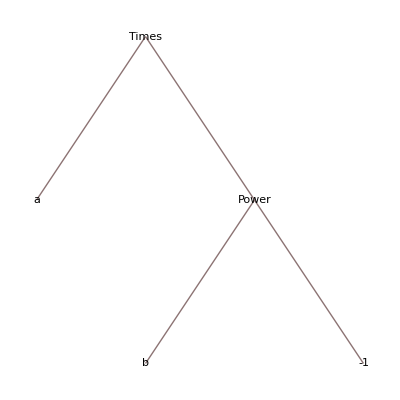

```mathematica
TreeForm[(a/b)]
```

```mathematica
a=N[2π]
```

6.28319

```mathematica
Cos[a]
```

1.

```mathematica
?a
```

Global`a

a=6.28319

```mathematica
f[x_]=1/(1+x)
```

1/(1+x)

```mathematica
f[.1]
```

0.909091

```mathematica
f[1]
```

1/2

```mathematica
f[α^2]
```

1/(1+α^2)

```mathematica
Clear[a,f]
```

```mathematica
rand=Random[]
```

0.342407

```mathematica
rand
```

0.342407

```mathematica
rand2:=Random[]
```

```mathematica
rand2
```

0.485404

```mathematica
rand2
```

0.049122

```mathematica
g[x_]:=x^3/;x≤0
g[x_]:=x/;0<x≤1
g[x_]:=Sin[x]/;x>1
```

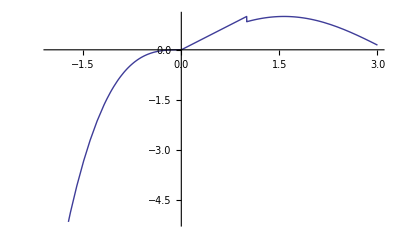

```mathematica
Plot[g[x],{x,-2,3}]
```

```mathematica
Piecewise[{{x^3,x≤0},{x,0<x≤1},{Sin[x],x>1}}]
```

Piecewise[{{x^3, x≤0}, {x, 0<x≤1}, {Sin[x], x>1}}]

```mathematica
f[x_]:=1+x+x^2
```

```mathematica
f[x_,y_]:=x+y
```

```mathematica
f[x_,y_,z_]:=1/(x+y-z)
```

```mathematica
?f
```

Global`f

f[x_]:=1+x+x^2
 
f[x_,y_,z_]:=1/(x+y-z)
 
f[x_,y_]:=x+y

```mathematica
Clear[f,g]
```

```mathematica
randLis1[n_]:=Table[Random[],{n}]
```

```mathematica
randLis1[5]
```

{0.796376,0.944086,0.40374,0.632428,0.569841}

```mathematica
randLis2[n_]:=(x=Random[];Table[x,{n}])
```

```mathematica
randLis2[5]
```

{0.319522,0.319522,0.319522,0.319522,0.319522}

```mathematica
randLis3[n_]:=(x:=Random[];Table[x,{n}])
```

```mathematica
randLis3[5]
```

{0.685522,0.0961688,0.36071,0.683852,0.336442}

```mathematica
randLis4[n_]=Table[Random[],{n}]
```

Table::iterb: Iterator {n} does not have appropriate bounds.

Table[Random[],{n}]

```mathematica
Clear[x,y,f,g]
```

```mathematica
f[n_]=Sum[(1+x)^j,{j,1,n}]
```

((1+x) (-1+(1+x)^n))/x

```mathematica
g[n_]:=Sum[(1+x)^j,{j,1,n}]
```

```mathematica
f[2]
```

((1+x) (-1+(1+x)^2))/x

```mathematica
g[2]
```

1+x+(1+x)^2

```mathematica
f[2]==g[2]
```

((1+x) (-1+(1+x)^2))/x==1+x+(1+x)^2

```mathematica
f[2]===g[2]
```

False

```mathematica
PrimeQ[144]
```

False

```mathematica
PrimeQ[3259]
```

True

```mathematica
PrimeQ[1969]
```

False

```mathematica
EvenQ[21]
```

False

```mathematica
IntegerQ[5/9]
```

False

```mathematica
NumericQ[π]
```

True

```mathematica
?∞
```

Information::notfound: Symbol "\[Infinity]" not found.

```mathematica
FullForm[({{1, 0}, {0, 1}})]
```

List[List[1,0],List[0,1]]

```mathematica
BaseForm[BitXor[2^^10101,2^^10011],2]
```

110_2

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
Sort[{b, 4,16,1,77,23, a, y, x}]
```

{1,4,16,23,77,a,b,x,y}

```mathematica
Table[i*j,{i,1,9},{j,1,9}]//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81

```mathematica
Table[i*j,{i,1,9},{j,1,9}]//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81)

```mathematica
Dimensions[{{{ 1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}}]
```

{2,3,2}

```mathematica
MatrixForm[{{{ 1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}}]
```

((1
2) | (3
4) | (5
6)
(a
b) | (c
d) | (e
f))

```mathematica
ArrayDepth[{{{ 1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}}]
```

3

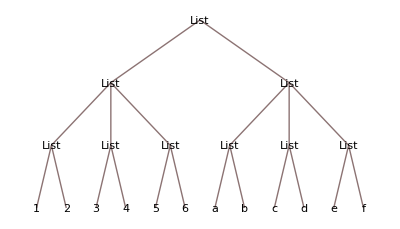

```mathematica
TreeForm[{{{ 1,2},{3,4},{5,6}},{{a,b},{c,d},{e,f}}}]
```

```mathematica
List[1,2]
```

{1,2}

```mathematica
Table[Range[0,i,2],{i,0,8,2}]
```

{{0},{0,2},{0,2,4},{0,2,4,6},{0,2,4,6,8}}

```mathematica
Table[Random[Integer],{10}]
```

{0,1,1,0,0,1,0,1,0,0}

```mathematica
Clear[f,g,x,y]
```

```mathematica
Array[f,5]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Table[f[i],{i,1,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Table[(-1)^Random[Integer],{10}]
```

{1,-1,1,-1,-1,1,-1,-1,1,-1}

```mathematica
Table[Random[Integer,{0,1}],{10}]
```

{0,0,1,1,1,0,1,0,0,0}

```mathematica
Table[Random[Integer,{-1,1}],{10}]
```

{0,1,-1,-1,1,1,1,0,-1,0}

```mathematica
Dimensions[{{{1,a},{4,d}},{{2,b},{3,c}}}]
```

{2,2,2}

```mathematica
Position[{5,7,5,2,1,4},5]
```

{{1},{3}}

```mathematica
Select[{1,4,1,5,9,2},EvenQ]
```

{4,2}

```mathematica
vec={2,3,7,8,1,4}
```

{2,3,7,8,1,4}

```mathematica
Part[vec,3]
```

7

```mathematica
vec[[3]]
```

7

```mathematica
vec[[{2,4}]]
```

{3,8}

```mathematica
(mat=Table[Subscript[a, i,j],{i,3},{j,3}])//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3)
a_(2,1) | a_(2,2) | a_(2,3)
a_(3,1) | a_(3,2) | a_(3,3))

```mathematica
mat[[2,1]]
```

a_(2,1)

```mathematica
mat[[All,2]]//MatrixForm
```

(a_(1,2)
a_(2,2)
a_(3,2))

```mathematica
mat
```

{{a_(1,1),a_(1,2),a_(1,3)},{a_(2,1),a_(2,2),a_(2,3)},{a_(3,1),a_(3,2),a_(3,3)}}

```mathematica
mat[[3]]
```

{a_(3,1),a_(3,2),a_(3,3)}

```mathematica
mat[[3]]//MatrixForm
```

(a_(3,1)
a_(3,2)
a_(3,3))

```mathematica
Take[{1,4,1,5,9,2},2]
```

{1,4}

```mathematica
Take[{1,4,1,5,9,2},-2]
```

{9,2}

```mathematica
Take[{1,4,1,5,9,2},{2,4}]
```

{4,1,5}

```mathematica
Take[{1,4,1,5,9,2},{-5,-3}]
```

{4,1,5}

```mathematica
Take[{1,4,1,5,9,2},{-5,4}]
```

{4,1,5}

```mathematica
Take[{1,4,1,5,9,2},{1,6,2}]
```

{1,1,9}

```mathematica
Drop[{1,4,1,5,9,2},2]
```

{1,5,9,2}

```mathematica
Drop[{1,4,1,5,9,2},-1]
```

{1,4,1,5,9}

```mathematica
Drop[{1,4,1,5,9,2},{3,5}]
```

{1,4,2}

```mathematica
Delete[{1,4,1,5,9,2},1]
```

{4,1,5,9,2}

```mathematica
Delete[{1,4,1,5,9,2},{{3},{4}}]
```

{1,4,9,2}

```mathematica
First[{1,4,1,5,9,2}]
```

1

```mathematica
Last[{1,4,1,5,9,2}]
```

2

```mathematica
Rest[{1,4,1,5,9,2}]
```

{4,1,5,9,2}

```mathematica
Sort[{3,1.7,π,-4,22/7}]
```

{-4,1.7,3,22/7,π}

```mathematica
Sort[{3,1.7,π,-4,22/7},Greater]
```

{22/7,π,3,1.7,-4}

```mathematica
Sort[{{2,c},{7,9},{e,f,g},{1,4.5},{x,y,z}}]
```

{{1,4.5},{2,c},{7,9},{e,f,g},{x,y,z}}

```mathematica
Reverse[{1,2,3,4,5}]
```

{5,4,3,2,1}

```mathematica
RotateLeft[{1,2,3,4,5}]
```

{2,3,4,5,1}

```mathematica
RotateRight[{1,2,3,4,5},2]
```

{4,5,1,2,3}

```mathematica
Partition[{1,4,1,5,9,2},2]
```

{{1,4},{1,5},{9,2}}

```mathematica
Partition[{1,4,1,5,9,2},1,2]
```

{{1},{1},{9}}

```mathematica
Partition[{1,4,1,5,9,2},2,1]
```

{{1,4},{4,1},{1,5},{5,9},{9,2}}

```mathematica
Transpose[{{1,2,3,4},{a,b,c,d}}]//MatrixForm
```

(1 | a
2 | b
3 | c
4 | d)

```mathematica
Transpose[{{1,2,3,4},{a,b,c,d},{i,ii,iii,iv}}]//MatrixForm
```

(1 | a | i
2 | b | ii
3 | c | iii
4 | d | iv)

```mathematica
Append[{1,2,3,4},5]
```

{1,2,3,4,5}

```mathematica
Prepend[{1,2,3,4},5]
```

{5,1,2,3,4}

```mathematica
Insert[{1,2,3,4},5,3]
```

{1,2,5,3,4}

```mathematica
Flatten[{{{3,1},{2,4}},{{5,3},{7,4}}}]
```

{3,1,2,4,5,3,7,4}

```mathematica
Flatten[{{{3,1},{2,4}},{{5,3},{7,4}}},1]
```

{{3,1},{2,4},{5,3},{7,4}}

```mathematica
MemberQ[Flatten[{{2,1,10},{9,5,7},{2,10,4},{10,1,9},{6,1,6}}],9]
```

True

```mathematica
list={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}}
```

{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}}

```mathematica
Transpose[list]
```

{{x1,x2,x3,x4,x5},{y1,y2,y3,y4,y5}}

```mathematica
Table[RandomChoice[{{1,0},{0,1},{-1,0},{0,-1}}],{10}]
```

{{0,1},{1,0},{0,1},{0,-1},{0,-1},{0,-1},{0,1},{-1,0},{-1,0},{0,1}}

```mathematica
Take[{a,b,c,d,e,f,g},{2,7,2}]
```

{b,d,f}

```mathematica
s={a,b,c,d};
p={3,2,4,1};
t=Table[s[[p[[k]]]],{k,1,Length[p]}]
```

{c,b,d,a}

```mathematica
r=Transpose[{p,s}]
```

{{3,a},{2,b},{4,c},{1,d}}

```mathematica
Part[Transpose[Sort[r]],2]
```

{d,b,a,c}

```mathematica
Join[{ 2,5,7,3},{d,a,e,j}]
```

{2,5,7,3,d,a,e,j}

```mathematica
Union[{4,1,2},{5,1,2}]
```

{1,2,4,5}

```mathematica
Complement[{4,1,2},{5,1,2}]
```

{4}

```mathematica
Intersection[{4,1,2},{5,1,2}]
```

{1,2}

```mathematica
Join[{x,y},List[z]]
```

{x,y,z}

```mathematica
p={1,2,3,4};  q={a,b,c,d};
Flatten[Transpose[Take[Transpose[{p,q}],{2,4,2}]]]
```

{2,4,b,d}

```mathematica
p={a,b,c,d};
q={a,b,e,f};
Complement[Union[p,q],Intersection[p,q]]
```

{c,d,e,f}

```mathematica
Head["The magic words are squeamish ossifrage."]
```

String

```mathematica
InputForm["Themagicwordsaresqueamishossifrage."]
```

"Themagicwordsaresqueamishossifrage."

```mathematica
s="The magic words are squeamish ossifrage."
```

The magic words are squeamish ossifrage.

```mathematica
StringLength[s]
```

40

```mathematica
StringReverse[s]
```

.egarfisso hsimaeuqs era sdrow cigam ehT

```mathematica
StringTake[s,3]
```

The

```mathematica
StringTake[s,-1]
```

.

```mathematica
StringTake[s,{1,10,2}]
```

Temgc

```mathematica
StringDrop[s,-1]
```

The magic words are squeamish ossifrage

```mathematica
StringPosition[s,"magic"]
```

{{5,9}}

```mathematica
StringInsert[s,"t",3]
```

Thte magic words are squeamish ossifrage.

```mathematica
StringReplace[s,"The"->"My"]
```

My magic words are squeamish ossifrage.

```mathematica
FullForm[RegularExpression["a.*"]]
```

RegularExpression["a.*"]

```mathematica
StringMatchQ["all in good time",RegularExpression["a.*"]]
```

True

```mathematica
StringCases["abc1, abd2, bcd3",RegularExpression["a.+?\\d"]]
```

{abc1,abd2}

```mathematica
?StringCases
```

StringCases[string,patt] gives a list of the substrings in "string" that match the string expression patt. 
StringCases[string,lhs->rhs] gives a list of the values of rhs corresponding to the substrings that match the string expression lhs. 
StringCases[string,p,n] includes only the first n substrings that match. 
StringCases[string,{p_1,p_2,…}] gives substrings that match any of the p_i. 
StringCases[{s_1,s_2,…},p] gives the list of results for each of the s_i.

```mathematica
Characters["abcde"]
```

{a,b,c,d,e}

```mathematica
Take[%,{2,3}]
```

{b,c}

```mathematica
StringJoin[%]
```

bc

```mathematica
ToCharacterCode["darwin"]
```

{100,97,114,119,105,110}

```mathematica
%-32
```

{68,65,82,87,73,78}

```mathematica
FromCharacterCode[%]
```

DARWIN

```mathematica
StringReplace["darwin",x->ToUpperCase[x]]
```

StringExpression::invld: Element x is not a valid string or pattern element in x.

StringReplace[darwin,x→ToUpperCase[x]]

```mathematica
ToUpperCase["darwin"]
```

DARWIN

```mathematica
s
```

The magic words are squeamish ossifrage.

```mathematica
s="abcde"
```

abcde

```mathematica
StringJoin[ToUpperCase[StringTake[s,{1,1}]],StringTake[s,-StringLength[s]+1]]
```

Abcde

```mathematica
?Dot
```

a.b.c or Dot[a,b,c] gives products of vectors, matrices and tensors.

```mathematica
s="789"
```

789

```mathematica
ToCharacterCode[s]
```

{55,56,57}

```mathematica
%-48
```

{7,8,9}

```mathematica
t=%
```

{7,8,9}

```mathematica
u=Reverse[Table[10^(i-1),{i,1,Length[t]}]]
```

{100,10,1}

```mathematica
t.u
```

789

```mathematica
PalindromeQ[str_]:=str==StringReverse[str]
```

```mathematica
PalindromeQ["refer"]
```

True